## Looking what remains if we put all constraints on the solutions

Firs we take the graph

```mathematica
g=Graph[EdgeList[EdgeAdd[WheelGraph[6,VertexLabels->"Name"],{2 <->7,3 <->7,3 <->8,4 <->8,7 <->8}]],GraphLayout->"TutteEmbedding",VertexLabels->"Name"];
```

From this graph we remove 3 edges to see what the remaining solutions are

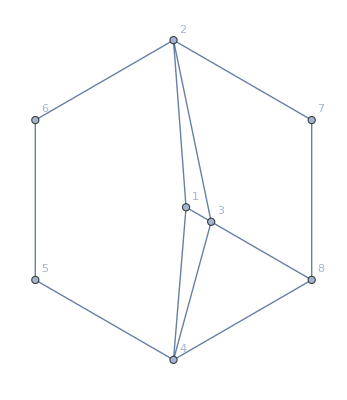

```mathematica
h=EdgeDelete[g,{3<->7,1<->6,1<->5}]
```

```mathematica
solutions2=Select[FindFullFormula[h],SymbolLevel[#]==4&]
```

{v1x28x35x467,v1x28x357x46,v1x258x3x467,v1x258x37x46,v1x258x367x4,v1x258x36x47,v1x24x367x58,v1x24x357x68,v18x2x35x467,v18x2x357x46,v18x25x3x467,v18x25x37x46,v18x25x367x4,v18x25x36x47,v18x24x367x5,v18x24x36x57,v18x24x357x6,v18x24x35x67,v17x28x35x46,v17x258x3x46,v17x258x36x4,v17x24x36x58,v17x24x35x68,v168x2x357x4,v168x2x35x47,v16x28x357x4,v167x28x35x4,v16x28x35x47,v167x258x3x4,v16x258x3x47,v168x25x3x47,v16x258x37x4,v168x25x37x4,v167x24x3x58,v168x24x3x57,v168x24x37x5,v16x24x37x58,v168x24x35x7,v16x24x357x8,v167x24x35x8,v158x2x3x467,v158x2x37x46,v158x2x367x4,v158x2x36x47,v15x28x3x467,v157x28x3x46,v15x28x37x46,v15x28x367x4,v157x28x36x4,v15x28x36x47,v157x24x3x68,v158x24x3x67,v158x24x37x6,v15x24x37x68,v158x24x36x7,v15x24x367x8,v157x24x36x8}

```mathematica
Length[solutions2]
```

57

Now we calculate the subsolutions  We impose the presence of all quadrilateral solutions first

```mathematica
quadrilateralSolutionsLeft=Select[solutions2,
(
PartitionHasPattern[SymbolToSets[#],{{2},{3,5},{4,6}}]||
PartitionHasPattern[SymbolToSets[#],{{2,4},{3},{4,5}}]||
PartitionHasPattern[SymbolToSets[#],{{2,5},{3,6},{4}}]||
PartitionHasPattern[SymbolToSets[#],{{2,4},{3,6},{5}}]||
PartitionHasPattern[SymbolToSets[#],{{2,4},{3,5},{6}}]
)
&]
```

{v1x28x35x467,v1x28x357x46,v1x258x367x4,v1x258x36x47,v1x24x367x58,v1x24x357x68,v18x2x35x467,v18x2x357x46,v18x25x367x4,v18x25x36x47,v18x24x367x5,v18x24x36x57,v18x24x357x6,v18x24x35x67,v17x28x35x46,v17x258x36x4,v17x24x36x58,v17x24x35x68,v168x24x35x7,v16x24x357x8,v167x24x35x8,v158x24x36x7,v15x24x367x8,v157x24x36x8}

## Now we look at some expected patterns

Next to the fact that we want all quadrilaterals, we also impose some more constraints.  Nodes 3 and 7 on the right must be different (because we want to join them with an edge).
On the left side we want 1 and 6 to be the same or 1 and 5

```mathematica
TableForm[Map[(Range[8]/.SymbolToColoring[#])&,Select[quadrilateralSolutionsLeft,
!PartitionHasPattern[SymbolToSets[#],{{3,7}}]&&
(PartitionHasPattern[SymbolToSets[#],{{1,6}}]||
PartitionHasPattern[SymbolToSets[#],{{1,5}}])&& !((PartitionHasPattern[SymbolToSets[#],{{1,6}}]&&
PartitionHasPattern[SymbolToSets[#],{{1,5}}]))
&]
], TableSpacing->{0, 0},TableHeadings->{Range[40], Range[8]}]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
1 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
2 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]
3 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
4 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]

We wanted a set that, when we add 3 and 7 on the rigth leaves both solutions on the left.  But we also want to destroy all solutions when we either add 1 and 6 or 1 and 5.
It seems that this solution set is all that is possible.  We can quickly verify this.  
1) Suppose we add 3 and 7.  This leaves us with the above 4 solutions.  Whatever edge we add (1-6 or 1-5) will always leave 2 solutions.  When we add the final one all solutions vanish.

But what if we first add 1-5 and 1-6.  Then we should still have a solution (which we don’t).  So the filter is not yet correct.

## I think it’s really “2 but not 3”

```mathematica
Right1[sym_]:=PartitionHasPattern[SymbolToSets[sym],{{3,7}}]
```

```mathematica
Right2[sym_]:=PartitionHasPattern[SymbolToSets[sym],{{3,8}}]
```

```mathematica
Left1[sym_]:=PartitionHasPattern[SymbolToSets[sym],{{1,6}}]
```

```mathematica
Left2[sym_]:=PartitionHasPattern[SymbolToSets[sym],{{1,5}}]
```

```mathematica
TableForm[Map[(Range[8]/.SymbolToColoring[#])&,Select[solutions2,
!Right1[#]
&]
], TableSpacing->{0, 0},TableHeadings->{Range[40], Range[8]}]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
1 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
2 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
3 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
4 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
5 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
6 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
7 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
8 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
9 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
10 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
11 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
12 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]
13 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]
14 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
15 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
16 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
17 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
18 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
19 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
20 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]
21 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
22 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
23 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]
24 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
25 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
26 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
27 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
28 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
29 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
30 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]
31 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
32 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0]
33 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]

```mathematica
TableForm[Map[(Range[8]/.SymbolToColoring[#])&,Select[solutions2,
(Right1[#]&&Left1[#]&&!Left2[#])||
(Right1[#]&&!Left1[#]&&Left2[#])
&]
], TableSpacing->{0, 0},TableHeadings->{Range[40], Range[8]}]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
1 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0]
2 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]
3 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]
4 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0]
5 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0]
6 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]
7 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]
8 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0]
9 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0]
10 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]
11 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]
12 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0]
13 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]
14 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]

```mathematica
TableForm[Map[(Range[8]/.SymbolToColoring[#])&,Select[solutions2,
(Right1[#]&&Left1[#]&&!Left2[#])||
(!Right1[#]&&Left1[#]&&Left2[#])
&]
], TableSpacing->{0, 0},TableHeadings->{Range[40], Range[8]}]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
1 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0]
2 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]
3 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]
4 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0]
5 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0]
6 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]
7 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]

```mathematica
TableForm[Map[(Range[8]/.SymbolToColoring[#])&,Select[solutions2,
(Right1[#]&&Left1[#]&&!Left2[#])||
(Right1[#]&&Left1[#]&&!Left2[#])
&]
], TableSpacing->{0, 0},TableHeadings->{Range[40], Range[8]}]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
1 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0]
2 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]
3 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]
4 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0]
5 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0]
6 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]
7 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]

```mathematica
TableForm[Map[(Range[8]/.SymbolToColoring[#])&,Select[solutions2,
(Right1[#]&&Left1[#]&&!Left2[#])||
(Right1[#]&&!Left1[#]&&Left2[#])||
(!Right1[#]&&Left1[#]&&Left2[#])
&]
], TableSpacing->{0, 0},TableHeadings->{Range[40], Range[8]}]
```

| 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8
1 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0]
2 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]
3 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]
4 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0]
5 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0]
6 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]
7 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]
8 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0]
9 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0]
10 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]
11 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]
12 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[1, 0, 0]
13 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]
14 | RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]

```mathematica
SymbolToColoring2[s_]:=Block[{sets=SymbolToSets[s],result={},colors={Red,Blue,Yellow,Green,Orange },colorpos=1},
Table[
Table[
AppendTo[result,v->Framed[v,FrameStyle->colors[[colorpos]]]]
,{v,block}
];
colorpos++;
If[colorpos>Length[colors],colorpos=1];
,{block,sets}
];
result
]
```

```mathematica
TableForm[Map[{Row[(Range[8]/.SymbolToColoring2[#])," "],If[Right1[#],"3==7",Style["3!=7",Red]],If[Left1[#],"1==6",Style["1!=6",Red]],If[Left2[#],"1==5",Style["1!=5",Red]]}&,Select[solutions2,
(Right1[#]&&Left1[#]&&!Left2[#])||
(Right1[#]&&!Left1[#]&&Left2[#])||
(!Right1[#]&&Left1[#]&&Left2[#])
&]
], TableSpacing->{1, 10}, TableDepth->1]
```

{  12345678,3==7,1==6,1!=5}
{  12345678,3==7,1==6,1!=5}
{  12345678,3==7,1==6,1!=5}
{  12345678,3==7,1==6,1!=5}
{  12345678,3==7,1==6,1!=5}
{  12345678,3==7,1==6,1!=5}
{  12345678,3==7,1==6,1!=5}
{  12345678,3==7,1!=6,1==5}
{  12345678,3==7,1!=6,1==5}
{  12345678,3==7,1!=6,1==5}
{  12345678,3==7,1!=6,1==5}
{  12345678,3==7,1!=6,1==5}
{  12345678,3==7,1!=6,1==5}
{  12345678,3==7,1!=6,1==5}

```mathematica
BooleanConvert[((a==b&&c≠d)||(a≠b&&c==d))&&!(a==b&&c==d)&&!(a≠b&&c≠d),"DNF"]
```

(a==b&&c≠d)||(a≠b&&c==d)

## Trying to get the criteria right

```mathematica
TableForm[Map[{Row[(Range[8]/.SymbolToColoring2[#])," "],If[Right1[#],"3==7",Style["3!=7",Red]],If[Left1[#],"1==6",Style["1!=6",Red]],If[Left2[#],"1==5",Style["1!=5",Red]]}&,Select[solutions2,
(Right1[#]&&((Left1[#]&&!Left2[#]))||((!Left1[#]&&Left2[#])))
&]
], TableSpacing->{1, 10}, TableDepth->1]
```

{  12345678,3==7,1==6,1!=5}
{  12345678,3==7,1==6,1!=5}
{  12345678,3==7,1==6,1!=5}
{  12345678,3==7,1==6,1!=5}
{  12345678,3==7,1==6,1!=5}
{  12345678,3==7,1==6,1!=5}
{  12345678,3==7,1==6,1!=5}
{  12345678,3!=7,1!=6,1==5}
{  12345678,3==7,1!=6,1==5}
{  12345678,3==7,1!=6,1==5}
{  12345678,3!=7,1!=6,1==5}
{  12345678,3!=7,1!=6,1==5}
{  12345678,3!=7,1!=6,1==5}
{  12345678,3==7,1!=6,1==5}
{  12345678,3==7,1!=6,1==5}
{  12345678,3!=7,1!=6,1==5}
{  12345678,3!=7,1!=6,1==5}
{  12345678,3!=7,1!=6,1==5}
{  12345678,3!=7,1!=6,1==5}
{  12345678,3==7,1!=6,1==5}
{  12345678,3==7,1!=6,1==5}
{  12345678,3!=7,1!=6,1==5}
{  12345678,3==7,1!=6,1==5}
{  12345678,3!=7,1!=6,1==5}

```mathematica
BoolToInt[b_]:=If[b,1,0]
```

```mathematica
TableForm[Map[{BoolToInt[Right1[#]]+BoolToInt[Left1[#]]+BoolToInt[Left2[#]],Row[(Range[8]/.SymbolToColoring2[#])," "],If[Right1[#],"3==7",Style["3!=7",Red]],If[Left1[#],"1==6",Style["1!=6",Red]],If[Left2[#],"1==5",Style["1!=5",Red]]}&,solutions2
]//Sort, TableSpacing->{1, 10}, TableDepth->1]
```

{0,  12345678,3!=7,1!=6,1!=5}
{0,  12345678,3!=7,1!=6,1!=5}
{0,  12345678,3!=7,1!=6,1!=5}
{0,  12345678,3!=7,1!=6,1!=5}
{0,  12345678,3!=7,1!=6,1!=5}
{0,  12345678,3!=7,1!=6,1!=5}
{0,  12345678,3!=7,1!=6,1!=5}
{0,  12345678,3!=7,1!=6,1!=5}
{0,  12345678,3!=7,1!=6,1!=5}
{0,  12345678,3!=7,1!=6,1!=5}
{0,  12345678,3!=7,1!=6,1!=5}
{0,  12345678,3!=7,1!=6,1!=5}
{0,  12345678,3!=7,1!=6,1!=5}
{1,  12345678,3!=7,1==6,1!=5}
{1,  12345678,3!=7,1==6,1!=5}
{1,  12345678,3==7,1!=6,1!=5}
{1,  12345678,3==7,1!=6,1!=5}
{1,  12345678,3!=7,1!=6,1==5}
{1,  12345678,3!=7,1!=6,1==5}
{1,  12345678,3!=7,1!=6,1==5}
{1,  12345678,3!=7,1!=6,1==5}
{1,  12345678,3==7,1!=6,1!=5}
{1,  12345678,3==7,1!=6,1!=5}
{1,  12345678,3!=7,1==6,1!=5}
{1,  12345678,3!=7,1==6,1!=5}
{1,  12345678,3==7,1!=6,1!=5}
{1,  12345678,3==7,1!=6,1!=5}
{1,  12345678,3!=7,1==6,1!=5}
{1,  12345678,3!=7,1==6,1!=5}
{1,  12345678,3!=7,1==6,1!=5}
{1,  12345678,3==7,1!=6,1!=5}
{1,  12345678,3==7,1!=6,1!=5}
{1,  12345678,3!=7,1!=6,1==5}
{1,  12345678,3!=7,1!=6,1==5}
{1,  12345678,3!=7,1!=6,1==5}
{1,  12345678,3!=7,1!=6,1==5}
{1,  12345678,3!=7,1!=6,1==5}
{1,  12345678,3!=7,1!=6,1==5}
{1,  12345678,3==7,1!=6,1!=5}
{1,  12345678,3==7,1!=6,1!=5}
{1,  12345678,3!=7,1==6,1!=5}
{1,  12345678,3!=7,1==6,1!=5}
{1,  12345678,3!=7,1==6,1!=5}
{2,  12345678,3==7,1==6,1!=5}
{2,  12345678,3==7,1==6,1!=5}
{2,  12345678,3==7,1!=6,1==5}
{2,  12345678,3==7,1!=6,1==5}
{2,  12345678,3==7,1!=6,1==5}
{2,  12345678,3==7,1==6,1!=5}
{2,  12345678,3==7,1==6,1!=5}
{2,  12345678,3==7,1==6,1!=5}
{2,  12345678,3==7,1!=6,1==5}
{2,  12345678,3==7,1!=6,1==5}
{2,  12345678,3==7,1!=6,1==5}
{2,  12345678,3==7,1!=6,1==5}
{2,  12345678,3==7,1==6,1!=5}
{2,  12345678,3==7,1==6,1!=5}